```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],
Cell[StyleData["Graphics"],
FontFamily->"Times New Roman",
FontColor->Black,
GraphicsBoxOptions->{
DefaultFrameStyle->Directive[FontSize->22,FontColor->Black,FontFamily->"Times New Roman"],
DefaultFrameTicksStyle->Directive[FontSize->16,FontColor->Black,FontFamily->"Times New Roman"],
DefaultLabelStyle ->Directive[FontColor->Black,FontFamily->"Times New Roman"],
DefaultTicksStyle->Directive[FontSize->16,FontColor->Black,FontFamily->"Times New Roman"]
}]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
SetOptions[{ListDensityPlot},LabelStyle->{14,Directive[Black,FontFamily->"Times New Roman"]}];
```

## Data plotting

```mathematica
dataPathList = 
{
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\plotData\\line15.csv",
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\plotData\\sierp2_v2.csv",
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\plotData\\triangle_v4.csv",
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\plotData\\triangle_niu4_v2.csv"
};
niuList = {2,4,6,4};
titleList = {"1D lattice","Sierpiński lattice", "triangular lattice","semi-triangular lattice"}
```

{1D lattice,Sierpiński lattice,triangular lattice,semi-triangular lattice}

```mathematica
Remove[makePlotIv2]
```

```mathematica
cols = {Black,Yellow,RGBColor[1,0.86,0]};
plotIDs = {"(a)","(b)","(c)","(d)"};
makePlotI[i_,dataPathList_:dataPathList,niuList_:niuList, titleList_:titleList, targetN_:15, plotIDs_:plotIDs]:=Block[{initialPhi,niu,phiData,nData,plotData,cf,data},data=Import[dataPathList[[i]],{"CSV","Data"},"SkipLines"->1,"IgnoreEmptyLines"->True];
initialPhi = 0.001;
niu = niuList[[i]];
phiData = {#1*niu,#2,#3}&@@@data;
nData = {#1*niu,#2,#4}&@@@data;
plotData = {#1*niu,#2,If[#3>=initialPhi,1,If[Abs[#4-targetN]/targetN>0.00001*1/targetN,2,0]]}&@@@data;
cf = Blend[{{0,cols[[1]]},{1,cols[[2]]},{2,cols[[3]]}},#]&;
ListDensityPlot[plotData,InterpolationOrder->0,ColorFunction->cf,ColorFunctionScaling->False,
FrameLabel->{{If[i==1,"μ/U",""],None},{"zJ/U",None}}, PlotLabel->Style[titleList[[i]],Black,FontSize->16],
ImageSize->220,AspectRatio->1, 
Epilog->{Inset[Style[plotIDs[[i]],FontFamily->"Times New Roman",FontSize->25],Scaled[{0.93,0.96}],{Right,Top}]}]]
```

#### Appendix

```mathematica
dataPathListA = 
{
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\plotData\\1d_l9_small_basis.csv",
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\plotData\\1d_l9_full_basis.csv",
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\plotData\\triangle_niu4_v3.csv",
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\plotData\\1d_l9_small_basis_more_iter.csv",
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\plotData\\1d_test.csv"
};
niuListA = {2,2,4,2,2};
(*titleListA = {"{p,q} = {7,3}", "{p,q} = {3,7}","{7,3} @ 7 sites","2 x 2 x 3 grid"}*)
targetNsA = {9,9,15,9,5}
```

{9,9,15,9,5}

```mathematica
Remove[makePlotIv2]
```

```mathematica
cols = {Black,Yellow,RGBColor[1,0.86,0]};
plotIDs = {"(a)","(b)","(c)","(d)"};
lgTriple = SwatchLegend[
cols,
Style[#,16,FontFamily->"Times New Roman"]&/@{"MI ","SF ","SF^*"},LegendFunction->"Frame",Background->White];
makePlotIv2[i_, plotID_:"",ylab_:True,xlab_:True,plotTitle_:False,dataPathList_:dataPathList,niuList_:niuList, titleList_:titleList, targetN_:15,idPos_:{0.96,0.9},legend_:False]:=Block[{initialPhi,niu,phiData,nData,plotData,cf,data},data=Import[dataPathList[[i]],{"CSV","Data"},"SkipLines"->1,"IgnoreEmptyLines"->True];
initialPhi = 0.001;
niu = niuList[[i]];
phiData = {#1*niu,#2,#3}&@@@data;
nData = {#1*niu,#2,#4}&@@@data;
plotData = {#1*niu,#2,If[#3>=initialPhi,1,If[Abs[#4-targetN]/targetN>0.999*1/targetN,2,0]]}&@@@data;
cf = Blend[{{0,cols[[1]]},{1,cols[[2]]},{2,cols[[3]]}},#]&;
ListDensityPlot[plotData,InterpolationOrder->0,ColorFunction->cf,ColorFunctionScaling->False,
FrameLabel->{{If[ylab,"μ/U",""],None},{If[xlab,"zJ/U",""],None}},
 PlotLabel->If[plotTitle,Style[titleList[[i]],Black,FontSize->16],None],
FrameTicksStyle->{If[ylab,Automatic,FontOpacity->0],If[xlab,Automatic,FontOpacity->0]},
ImageSize->{Automatic,240},AspectRatio->1, 
Epilog->{Inset[Style[plotID,FontFamily->"Times New Roman",FontSize->25],Scaled[idPos],{Right,Top}],If[legend,Inset[lgTriple,Scaled[{0.96,0.96}],{Right,Top}]]}]]
```

```mathematica
N@1/(15)
```

0.0666667

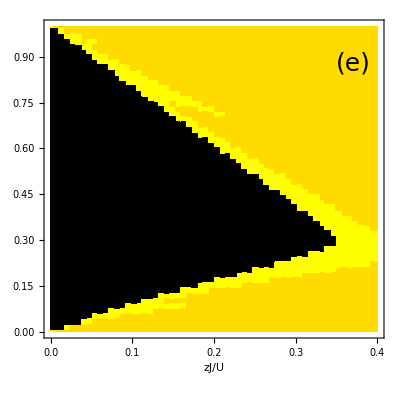

```mathematica
p1D15phi = makePlotIv2[1,"(e)",False,True]
```

```mathematica
Remove[makePlotNoverV]
```

```mathematica
colsN={Purple,Red,Orange,Yellow,RGBColor[0.69,0.98,0.]};
minNoV =0.7;
maxNoV = 1.6;
cfN = Block[{min=minNoV, max=1.35},Evaluate[Blend[{{min,colsN[[1]]},{(max-min)*3/7+min,colsN[[2]]},{(max-min)*4/7+min,colsN[[3]]},{max,colsN[[4]]},{maxNoV,colsN[[5]]}},#]]&];
```

```mathematica
colsN={Purple,RGBColor[0.65,0.,0.34],Red,Orange,Yellow,RGBColor[0.69,0.98,0.]};
minNoV =0.7;
maxNoV = 1.6;
cfN = Block[{min=minNoV, max=1.35},Evaluate[Blend[{{min,colsN[[1]]},{0.9,colsN[[2]]},{1,colsN[[3]]},{1.1,colsN[[4]]},{max,colsN[[5]]},{maxNoV,colsN[[6]]}},#]]&];
makePlotNoverV[i_, plotID_:"",ylab_:True,xlab_:True,plotTitle_:False,dataPathList_:dataPathList,niuList_:niuList, titleList_:titleList, targetN_:15]:=Block[{initialPhi,niu,phiData,nData,plotData,cf,data},data=Import[dataPathList[[i]],{"CSV","Data"},"SkipLines"->1,"IgnoreEmptyLines"->True];
initialPhi = 0.001;
niu = niuList[[i]];
phiData = {#1*niu,#2,#3}&@@@data;
nData = {#1*niu,#2,#4}&@@@data;
plotData = {#1*niu,#2,#4/(targetN)}&@@@data;
cf = cfN;
ListDensityPlot[plotData,InterpolationOrder->0,ColorFunction->cf,ColorFunctionScaling->False,
FrameLabel->{{If[ylab,"μ/U",""],None},{If[xlab,"zJ/U",""],None}},
FrameTicksStyle->{If[ylab,Automatic,FontOpacity->0],If[xlab,Automatic,FontOpacity->0]},
ImageSize->{Automatic,240},AspectRatio->1, 
Epilog->{Inset[Style[plotID,FontFamily->"Times New Roman",FontSize->25],Scaled[{0.96,0.9}],{Right,Top}]}]]
```

Blend::argp: #1 should be a real number.

```mathematica
makePlotFlucs[i_, plotID_:"",ylab_:True,xlab_:True,plotTitle_:False,dataPathList_:dataPathList,niuList_:niuList, titleList_:titleList, targetN_:15]:=Block[{initialPhi,niu,phiData,nData,plotData,cf,data},data=Import[dataPathList[[i]],{"CSV","Data"},"SkipLines"->1,"IgnoreEmptyLines"->True];
initialPhi = 0.001;
niu = niuList[[i]];
phiData = {#1*niu,#2,#3}&@@@data;
nData = {#1*niu,#2,#4}&@@@data;
plotData = {#1*niu,#2,#5/(targetN)}&@@@data;
ListDensityPlot[plotData,InterpolationOrder->0,ColorFunction->Automatic,ColorFunctionScaling->True,
FrameLabel->{{If[ylab,"μ/U",""],None},{If[xlab,"zJ/U",""],None}},
FrameTicksStyle->{If[ylab,Automatic,FontOpacity->0],If[xlab,Automatic,FontOpacity->0]},
ImageSize->{Automatic,240},AspectRatio->1, 
Epilog->{Inset[Style[plotID,FontFamily->"Times New Roman",FontSize->25],Scaled[{0.96,0.9}],{Right,Top}]}]]
```

```mathematica
p1D15n = (*Legended[*)makePlotFlucs[2,"(b)",False,True,False,dataPathListA,niuListA,None, targetNsA[[1]]]
```

-Graphics-

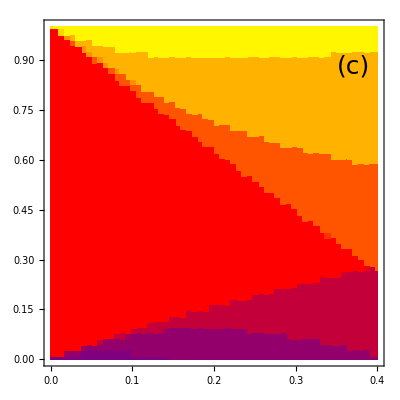

```mathematica
p1D9n = (*Legended[*)makePlotNoverV[1,"(c)",False,False](*,Placed[BarLegend[{cfN,{0.75,maxNoV}},LegendMarkerSize->200,TicksStyle->Directive[FontSize->14,FontColor->Black,FontFamily->"Times New Roman"]],{1,.553}]]*)
```

```mathematica
p1D15phi = makePlotIv2[1,"(e)",False,True]
```

-Graphics-

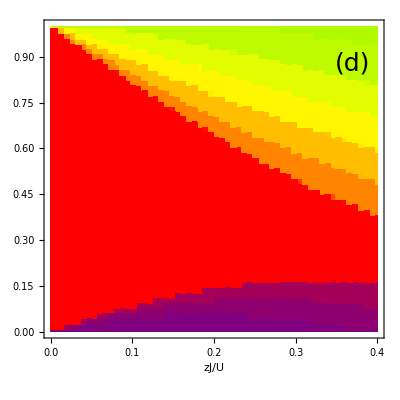

```mathematica
p1D15n = (*Legended[*)makePlotNoverV[2,"(d)",False,True,False,dataPathListA,niuListA,None, targetNsA[[2]]](*,Placed[BarLegend[{cfN,{0.75,1.65}},LegendMarkerSize->200,TicksStyle->Directive[FontSize->14,FontColor->Black,FontFamily->"Times New Roman"]],{1,.553}]]*)
```

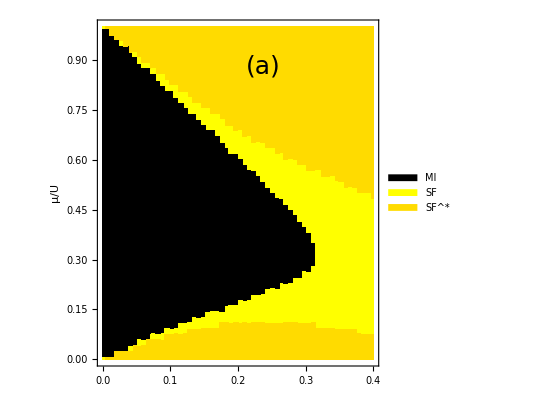

```mathematica
p1D9small = makePlotIv2[1,"(a)",True,False,False,dataPathListA,niuListA,None, targetNsA[[1]],{0.65,0.9},True]
```

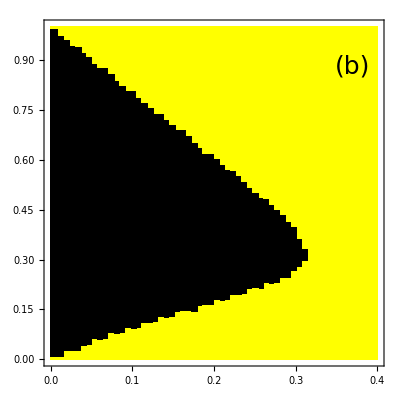

```mathematica
p1D9phi = makePlotIv2[2,"(b)",False,False,False,dataPathListA,niuListA,None, targetNsA[[2]]]
```

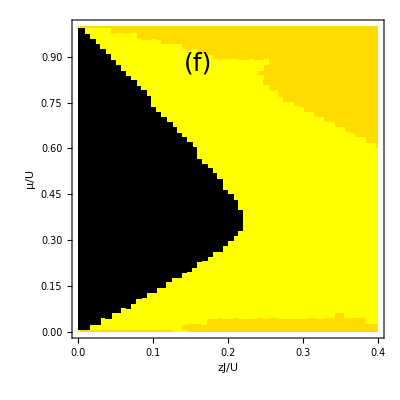

```mathematica
pTrNiu4 = makePlotIv2[3,"(f)",True,True,False,dataPathListA,niuListA,None, targetNsA[[3]],{0.45,0.9}]
```

```mathematica
pAppGridNoBar = Rasterize[GraphicsGrid[{{p1D9small,p1D9phi, p1D9n},{pTrNiu4,p1D15phi,p1D15n}},Spacings->{-43,-45},ImagePadding->{{22, 22}, {0, 22}},ImageSize->{Automatic,400}],ImageResolution->300,ImageSize->{Automatic,400}]
```

```mathematica
bar2 = Graphics[Rasterize[#,ImageResolution->300]&@BarLegend[{cfN,{minNoV,maxNoV}},LegendMarkerSize->220,Ticks->Table[If[Mod[10x,1]==0,{x,N@x, 0.03},{x,"",0.01}],{x,7/10,16/10,2/100}],TicksStyle->Directive[Black,FontSize->12,FontColor->Black,FontFamily->"Times New Roman"],LegendLabel->Style["n/V_C",FontSize->18,FontFamily->"Times New Roman"]],ImageSize->{Automatic,320}]
```

-Graphics-

```mathematica
bar2good =Show[Graphics[{White,Rectangle[{0,0},{AbsoluteOptions[bar2,ImageSize][[1,2,1]],400}]},ImageSize->{AbsoluteOptions[bar2,ImageSize][[1,2,1]],400}],
Epilog->Inset[bar2,Scaled[{0.5,1}],Scaled[{0.5,1}]]]
```

-Graphics-

```mathematica
g=Graph[ResourceFunction["TriangularGridGraph"][4],EdgeStyle->Thickness[0.03]];
pg4b =Graph[addGreen[g,4,0.15,False,0.03],ImageSize->100,ImagePadding->0,Background->White,Frame->True,FrameStyle->Directive@{Black,Thickness[0.03]}]
```

-Graphics-

```mathematica
pAppendixBar = GraphicsRow[{pAppGridNoBar,bar2good},Spacings->-1,Epilog->Inset[pg4b,Scaled[{0.195,0.32}],Scaled[{0.,0.}],75]]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\fig13.pdf",pAppendixBar]
```

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs\fig13.pdf

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\Magisterium\\MSC-plots\\fig5.pdf",pAppendixBar]
```

C:\Users\kamil\OneDrive\Documents\DIPCwork\Magisterium\MSC-plots\fig5.pdf

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs_svg\\appendix_grid.svg",pAppendixBar]
```

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs_svg\appendix_grid.svg

```mathematica
p1D15 = GraphicsRow[Rasterize[#,ImageResolution->300]&/@{pT15phi,pT15n},ImageSize->250*2,Spacings->-1]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\appendix_1D_15.pdf",p1D15]
```

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs\appendix_1D_15.pdf

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs_svg\\appendix_1D_15.svg",p1D15]
```

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs_svg\appendix_1D_15.svg

```mathematica
p1D9phi = makePlotIv2[1,"(a)"]
```

### Normal

```mathematica
Table[makePlotI[i],{i,Length@dataPathList}]
```

```mathematica
ps = Table[makePlotI[i],{i,3}];
gs = {pg1,pg2,pg3};
lg = SwatchLegend[
cols,
Style[#,16,FontFamily->"Times New Roman"]&/@{"MI ","SF ","SF^*"},LegendFunction->"Frame",Background->White];
plot = Rasterize[#,ImageResolution->300]&@GraphicsGrid[{gs,ps},Spacings->{-30,0},Epilog->{Inset[lg,Scaled[{1.15,-0.08}]]},ImageSize->220*3-100]
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs_svg\\homo_MI_SF.svg",plot]
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\homo_MI_SF.pdf",plot]
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\homo_MI_SF.png",plot]
```

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs_svg\homo_MI_SF.svg

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs\homo_MI_SF.pdf

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs\homo_MI_SF.png

```mathematica
lg = SwatchLegend[
cols,
Style[#,16,FontFamily->"Times New Roman"]&/@{"|Φ| = 0","|Φ| > 0","n > 1"},
(*LegendLabel->Style["Fitted functions",12,FontFamily->"Times New Roman"],*)LegendFunction->"Frame"
]
```

```mathematica
cols = {Black,Yellow,Yellow};
ps = Table[makePlotI[i],{i,3}];
cols = {Black,Yellow,RGBColor[1,0.86,0]};
gs = {pg1,pg2,pg3};
lg = SwatchLegend[
cols,
Style[#,16,FontFamily->"Times New Roman"]&/@{"MI ","SF "},LegendFunction->"Frame",Background->White];
plot = Rasterize[#,ImageResolution->300]&@GraphicsGrid[{gs,ps},Spacings->{{0,-30,-30,0},{0,0,0}},Epilog->{Inset[lg,Scaled[{1.16,-0.15}]]},ImageSize->220*3-100]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs_svg\\simple_homo_MI_SF.svg",plot]
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\simple_homo_MI_SF.pdf",plot]
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\simple_homo_MI_SF.png",plot]
```

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs_svg\simple_homo_MI_SF.svg

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs\simple_homo_MI_SF.pdf

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs\simple_homo_MI_SF.png

```mathematica
avgNeibOld[g_,v_]:=Block[{edgesForV, neighbors,vertexPositions,neighborPositions,averagePosition},
edgesForV=Select[EdgeList[g],MemberQ[#,v]&];

(*Extract neighbors from these edges by removing v itself*)
neighbors=First@Flatten[DeleteCases[#,v]]&/@edgesForV;
vertexPositions=GraphEmbedding[g];
(*Get the positions of the neighbors*)neighborPositions=vertexPositions[[neighbors]];

(*Compute the average position of the neighbors*)
averagePosition=Mean[neighborPositions]]
avgNeib[g_,v_]:=Block[{edgesForV,neighbors,vertexPositions,neighborPositions,averagePosition,vertexList,neighborIndices},vertexList=VertexList[g];(*Get the full list of vertices*)vertexPositions=GraphEmbedding[g];(*Get the corresponding positions*)(*Find all edges connected to v*)edgesForV=Select[EdgeList[g],MemberQ[#,v]&];
(*Extract neighbors by removing v itself*)neighbors=Complement[Flatten[List@@@edgesForV,1],{v}];
(*Find indices of these neighbors in VertexList*)neighborIndices=FirstPosition[vertexList,#,Missing[]]&/@neighbors;
neighborIndices=DeleteCases[neighborIndices,Missing[]];
(*Remove missing cases*)(*Get positions of the valid neighbors*)neighborPositions=vertexPositions[[Flatten[neighborIndices]]];
(*Compute the average position*)Mean[neighborPositions]]
```

```mathematica
Remove[addGreen]
```

```mathematica
Max[#]-Min[#]&@(Transpose[{{1,-2},{0.1,-2}}][[1]])
```

0.9

```mathematica
Min[{{1,-2},{0.1,-2}}]
```

-2

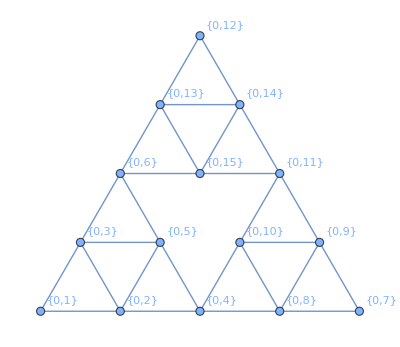

```mathematica
Graph[MeshConnectivityGraph@SierpinskiMesh[2],VertexLabels->Automatic]
```

```mathematica
Remove[addGreen];
addGreen[ogG_,targetNiu_,dd_:0.1, sierpDegs_:False,greenThickness_:0.015]:=
Block[{g=ogG,boundaryNodes, v, missing, newPoints,oldCords, newCords,degList,newEdges,existingVertices,existingEdgeStyle, existingVertexStyle},
g = Graph[g, VertexCoordinates->(Mean[GraphEmbedding[g]]+#&/@GraphEmbedding[g])/(Max[#]-Min[#]&@(Transpose[GraphEmbedding[g]][[1]]))];
boundaryNodes=Select[VertexList[g],VertexDegree[g,#]<targetNiu&];
Do[
v = boundaryNodes[[j]];
missing = targetNiu - VertexDegree[g,v];
newPoints = Range[VertexCount@g+1,VertexCount@g+missing ];
(*If[v[[0]]==List, newPoints = {0,#}&/@newPoints];*)
oldCords = (GraphEmbedding[g])[[First@FirstPosition[VertexList[g],v]]];
degList = {-30,30};
If[missing == 4, degList = {-90,-30,30,90}];
If[missing == 4 &&  targetNiu == 7, degList = {-60,-20,20,60}]; (*special for hyperbolic*)
If[missing == 1, degList = {0}];
If[missing == 3, degList = {-45,0,45}];
If[missing == 2 && sierpDegs,
If[v == {0,1},
(*adjust manually to the bigger lattice*)
degList = -{30,90},
degList = -{-30,-90}
]
];
If[missing<=0,Continue[]];
degList = degList*Degree;
newCords = Table[dd*(RotationMatrix[deg].(oldCords - avgNeib[g,v]))/Norm[oldCords - avgNeib[g,v]]+oldCords,{deg, degList}];
newEdges = Table[UndirectedEdge[v,p],{p,newPoints}];
existingVertices=VertexList[g];
existingEdgeStyle=EdgeStyle/. Options[g,EdgeStyle];
If[existingEdgeStyle==Automatic,existingEdgeStyle={}];
existingVertexStyle=VertexStyle/. Options[g,VertexStyle];
If[existingVertexStyle==Automatic,existingVertexStyle={}];
g=Graph[
Join[existingVertices,newPoints],
Join[EdgeList[g],newEdges],
VertexCoordinates->Join[GraphEmbedding[g], newCords],
VertexStyle->Join[existingVertexStyle,Table[p->Directive[Opacity[0],EdgeForm[None]], {p,newPoints}]],
EdgeStyle->Join[existingEdgeStyle,Table[e->{Green,Thickness[greenThickness]},{e,newEdges}]],ImageSize->180,ImagePadding->{{40,0}, {0,0}}
],
{j,Length@boundaryNodes}
];
Return[g]
]
```

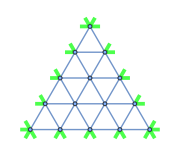

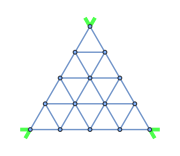

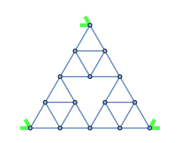

-Graphics-

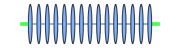

```mathematica
g=ResourceFunction["TriangularGridGraph"][4];
pg3 =addGreen[g,6]
g=ResourceFunction["TriangularGridGraph"][4];
pg4 =addGreen[g,4]
g=MeshConnectivityGraph@SierpinskiMesh[2];
pg2 =addGreen[g,4,0.1,True]
pg2 = Graph[pg2,ImagePadding->{{40,0},{AbsoluteOptions[pg3, ImageSize][[1,2,2]]-AbsoluteOptions[pg2, ImageSize][[1,2,2]],0}}]
g=Graph[Range[#],Table[UndirectedEdge[i,i+1],{i,#-1}],VertexCoordinates->Transpose[{Range[#],Range[#]*0}]]&@15;
pg1=addGreen[g,2]
```

### Tobias’

```mathematica
(*Parameters*)z=1; (*coordination number,e.g.4 for 2D square lattice*)
nMax=3; (*maximum number of lobes*)
res=200; (*resolution of the grid*)

(*Define the critical hopping function for given mu/U and filling n*)
isMott[muOverU_,tOverU_]:=Module[{mu=muOverU,t=tOverU,boundary,n},For[n=1,n<=nMax,n++,If[mu>n-1&&mu<n,boundary=1/(z ((n+1)/(n-mu)+n/(mu-(n-1))));
If[t<boundary,Return[0]] (*Mott insulator*)];];
Return[1] (*Superfluid*)];

(*Generate a grid of values*)
ress = Flatten[Table[{mu, J, isMott[mu,J]},{mu,0,nMax,0.005},{J,0,0.2,0.002}],1];
```

```mathematica
ListDensityPlot[ress,InterpolationOrder->0,ColorFunction->(Blend[{{0,Black},{1,Yellow}},#]&), FrameLabel->{"μ/U","z/U"},Epilog->{Inset[lg,Scaled[{0.85,0.85}]]}]
```

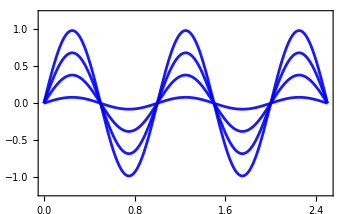

```mathematica
Show[Plot[Table[a Sin[2Pi x],{a,0.08,1,0.3}],{x,0,2.5},PlotStyle->Directive[Blue,Opacity[0.9]],PlotRange->{{0,2.5},{-1.2,1.2}},Axes->False,Frame->True,FrameStyle->Black,FrameTicks->None]]
```

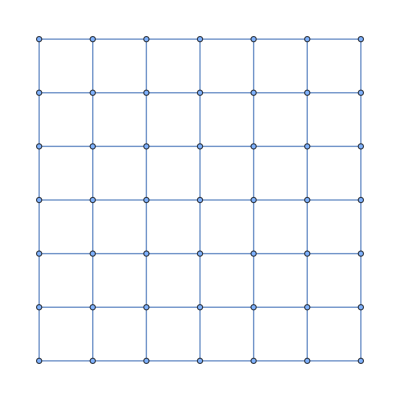

```mathematica
GridGraph[{7,7}]
```

```mathematica
spec = Sort@N@Eigenvalues@-N@AdjacencyMatrix@MeshConnectivityGraph@SierpinskiMesh[7];
```

Eigenvalues::arh: Because finding 3282 out of the 3282 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

```mathematica
(*spec = Sort@N@Eigenvalues@-N@AdjacencyMatrix@GridGraph[{50,50}];*)
```

Eigenvalues::arh: Because finding 2500 out of the 2500 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

```mathematica
(*Define the range for mu and J*)muValues=Table[x,{x,0.00001,0.999,1/500}];
jValues=Table[x,{x,0,0.2,0.2/500}];

(*Compute dd2 matrix*)
dd2=Table[Module[{gnum,matrix},
gnum=(mu+1)/(mu (1-mu));
matrix=N[(1/gnum)]*N@ ConstantArray[1,Length@spec]+J spec;
Min[Abs[matrix]]/Max[Abs[matrix]]],{J,jValues},{mu,muValues}];
```

```mathematica
cf = Blend[{{0,Yellow},{0.20,Yellow},{0.25,Red},{0.70,Black},{1,Black}},#]&
```

Blend[{{0,Yellow},{0.2,Yellow},{0.25,Red},{0.7,Black},{1,Black}},#1]&

```mathematica
cf = Blend[{{0,Yellow},{0.20,Yellow},{0.21,Black},{0.70,Black},{1,Black}},#]&
```

Blend[{{0,Yellow},{0.2,Yellow},{0.21,Black},{0.7,Black},{1,Black}},#1]&

```mathematica
BarLegend[cf]
```

```mathematica
LogarithmicScaling[x_,min_,max_]:=Log[x/min]/Log[max/min]
plotter[min_,max_,NumberOfTicks_]:=Legended[ListDensityPlot[Flatten[Table[{(*z=4*)4*jValues[[jj]],muValues[[mmu]],dd2[[jj,mmu]]},{jj,1,Length[jValues]},{mmu,1,Length[muValues]}],1],ColorFunctionScaling->False,PlotRange->Full,ColorFunction->(cf[LogarithmicScaling[#,min,max]]&),PlotLegends->None,FrameLabel->{{"μ/U",None},{"zJ/U",None}},(* PlotLabel->Style["",Black,FontSize->16],*)
ImageSize->{Automatic,240},AspectRatio->1],Placed[BarLegend[{cf,{0,1}},LegendMarkerSize->200,Ticks->({LogarithmicScaling[#,min,max],ScientificForm[#,2]}&/@(min (max/min)^Range[0,1,1/NumberOfTicks])), TicksStyle->Directive[FontSize->14,FontColor->Black,FontFamily->"Times New Roman"]],{1,.553}]]
```

```mathematica
pTob = plotter[10^-2,10^0,4]
```

-Graphics-

```mathematica
xs = Table[x,{x,0.001,0.999999,0.001}];
dats = Table[Block[{y1},
y1=-#*(1-#)/(spec[[j]]*(1+#))&/@xs;
Transpose[{(*z=4*)4*y1,xs}]],{j,{1,(*243,244,*)729,730}}];
```

```mathematica
pTobWLines = Rasterize[Show[pTob,ListLinePlot[dats,PlotStyle->Directive[Dashed,Black]] ,ImageSize->{Automatic,240},
Epilog->{Inset[Style["(b)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.95,0.975}],{Right,Top}]}
],ImageResolution->300,ImageSize->{Automatic,240}]
```

-Graphics-

```mathematica
pTobSpec = Show[Rasterize[ListPlot[Transpose@{Range[0,Length@spec - 1],spec},PlotStyle->Black,PlotMarkers->{Automatic,7}, FrameLabel->{"Eigenstate number","Energy"},Frame->True,ImageSize->{Automatic,225},AspectRatio->0.95,Epilog->{Inset[Style["(a)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.04,0.99}],{Left,Top}],
Dashed,InfiniteLine[{0,spec[[#]]},{1,0}]&/@{1,(*243,244,*)729,730}},
FrameTicks->{{Automatic, Automatic},{Table[If[Mod[x,1000]==0,{x,x, 0.02},{x,"",0.01}],{x,0,3500,100}],Automatic}}
],ImageResolution->300],ImageSize->{Automatic,232}]
```

-Graphics-

```mathematica
pTobFin = GraphicsRow[{pTobSpec,pTobWLines},Spacings->1,ImageSize->{Automatic,270}]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\lobes_v2.png",pTobFin]
```

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs\lobes_v2.png

```mathematica
y1=-#*(1-#)/(spec[[1]]*(1+#))&/@xs;
```

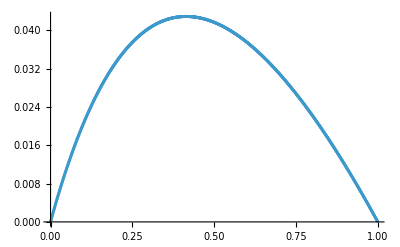

```mathematica
ListPlot[Transpose@{xs,y1}]
```

```mathematica
y1=-#*(1-#)/(spec[[1]]*(1+#))&/@xs;
y2=-x.*(1-x)./(spec(243).*(1+x));
y3=-x.*(1-x)./(spec(244).*(1+x));
y4=-x.*(1-x)./(spec(729).*(1+x));
y5=-x.*(1-x)./(spec(730).*(1+x));
```

```mathematica
LogarithmicScaling[x_,min_,max_]:=Log[x/min]/Log[max/min]
plotter[min_,max_,NumberOfTicks_]:=ListDensityPlot[Flatten[Table[{(*z=4*)4*jValues[[jj]],muValues[[mmu]],dd2[[jj,mmu]]},{jj,1,Length[jValues]},{mmu,1,Length[muValues]}],1],ColorFunctionScaling->False,PlotRange->Full,ColorFunction->(cf[LogarithmicScaling[#,min,max]]&),PlotLegends->BarLegend[{cf,{0,1}},LegendMarkerSize->220,Ticks->({LogarithmicScaling[#,min,max],ScientificForm[#,2]}&/@(min (max/min)^Range[0,1,1/NumberOfTicks]))],FrameLabel->{{"μ/U",None},{"zJ/U",None}},(* PlotLabel->Style["",Black,FontSize->16],*)
ImageSize->250,AspectRatio->1]
pTob = plotter[10^-2,10^0,4];
Legended[pTob,Placed[BarLegend[{ColorData[{"BlueGreenYellow",{-1,1}}],{-1,1}},LabelStyle->{FontSize->13,Blue,Bold},LegendMarkerSize->250.],{1,.51}]]
```

#### Translation plot

```mathematica
{{x,-0.653},-0.8,-0.45},{{y,-2.6842},-2.7,-2.55},{{siz,5.566},5.3,5.8}
```

```mathematica
pG = Graph[MeshConnectivityGraph[SierpinskiMesh[5]],ImageSize->1000,VertexSize->0.2,

VertexStyle->Directive[Opacity[1]],EdgeStyle->Directive[RGBColor[127/300,178/300,1],Thickness[0.002],Opacity[1]],Background->Opacity[0,White]];
pGcut=Graphics[Inset[pG,ImageScaled[{-0.653,-2.6842}],ImageScaled[{0,0}],ImageScaled[5.566]],AspectRatio->0.41,ImageSize->400,Background->None]

(*Graphics[Inset[pG,ImageScaled[{-0.514,-0.638}],ImageScaled[{0,0}],ImageScaled[3.878]],AspectRatio->1.3,ImageSize->400,Background->None]*)
```

-Graphics-

```mathematica
pgTest=-Graphics-
```

-Graphics-

```mathematica
pGGreen = Graph[MeshConnectivityGraph[SierpinskiMesh[5]],ImageSize->1000,VertexSize->0.2,Background->Opacity[0,White],EdgeStyle->Directive[{Green,Thickness[0.002]}],VertexStyle->Green];
pGcutGreen=Graphics[Inset[pGGreen,ImageScaled[{-0.514,-0.638}],ImageScaled[{0,0}],ImageScaled[3.878]],AspectRatio->1.3,ImageSize->400,Background->None]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\translate_cut.png",pGcut,ImageResolution->300,Background->None]
```

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\translate_cut.png

```mathematica
Show[pGcutGreen,Show[pGcut,PlotRange->{-1,1}]]
```

-Graphics-

```mathematica
Manipulate[Graphics[Inset[pG,ImageScaled[{x,y}],ImageScaled[{0,0}],ImageScaled[siz]],AspectRatio->0.41],{{x,-0.653},-0.8,-0.45},{{y,-2.6842},-2.7,-2.55},{{siz,5.566},5.3,5.8}]
```

```mathematica
Export[""]
```

```mathematica
Graph[MeshConnectivityGraph[SierpinskiMesh[6]],ImageSize->800,VertexSize->0.2]
```

### Hyperbolic

```mathematica
hyperbolicRotation[z_,{c_,t_}]:=With[{w=((z-c) E^(I t))/(1-z Conjugate[c])},(c+w)/(1+w Conjugate[c])]

hyperbolicReflection[coords_,n_,m_]/;(1/n+1/m<1/2):=Nest[Append[#,hyperbolicRotation[#[[-2]],{#[[-1]],2 π/m}]]&,coords,n-2]

seedCoords[n_,m_]/;(1/n+1/m<1/2):=Block[{r,v,s=Sin[π/n]^2  Sec[π/m]^2},r=s/(1-s);
v=Sqrt[1+2 r-2 Sqrt[r (1+r)] Sin[π (1/n+1/m)]] Exp[I π/n];
NestList[hyperbolicRotation[#,{0,-2 π/n}]&,v,n-1]]

growCoords[coords_,m_]:=With[{n=Length[coords]},Map[hyperbolicReflection[#,n,m]&]@Reverse[Partition[coords,2,1,1],2]]
hCoords[n_,m_,k_,op:(Automatic|"Poincare"|"Beltrami"):"Poincare",pr_:Automatic]/;(1/n+1/m<1/2):=Module[{opr=op/. {Automatic|"Poincare"->Identity,"Beltrami"->(2 #/(1+Abs[#]^2)&)}},Rationalize[Map[ReIm@*opr,NestList[p|->Flatten[growCoords[#,m]&/@p,1],{N@seedCoords[n,m]},k],{2}],pr/. Automatic->10^-5]]
indexCoords=Association@*DeleteDuplicatesBy[Sort@*First]@*(Thread[ArrayComponents[#,2]->#]&)@*Last;

getEdgeList=DeleteDuplicatesBy[Sort]@*Apply[Join]@*Map[MapApply[UndirectedEdge]@Partition[#,2,1,1]&]@*Keys;

getVertexCoords=DeleteDuplicates@*Apply[Join]@*KeyValueMap[Thread[#->#2]&];
GraphComputation`GraphPropertyChart;

poincareESF=GraphComputation`GraphChartDump`geo[.99 First[#],.99 Last[#],"segment"]&;

poincareLine=GraphComputation`GraphChartDump`geo[.99 First[#],.99 Last[#],"line"]&;
hyperbolicGraph[n_,m_,iter_:1,layout:(Automatic|"Poincare"|"Beltrami"):"Poincare",pr_:Automatic,opts:OptionsPattern[]]/;(1/n+1/m<1/2):=Module[{vl,el,vc,coords=indexCoords@hCoords[n,m,iter,layout,pr/. Automatic->10^-3]},vc=getVertexCoords@coords;
el=getEdgeList@coords;
vl=Range@Length@vc;
Graph[vl,el,VertexCoordinates->vc,EdgeShapeFunction->poincareESF,opts]]
```

```mathematica
installPythonPackage[packageName_]:=ExternalEvaluate[{"Shell", "Target" :> $SystemShell}, "C:\\Users\\kamil\\AppData\\Roaming\\Wolfram\\ApplicationData\\ExternalEvaluate\\Python\\Venv\\Default\\Scripts\\python.exe" -> {"-m", "pip", "install",packageName}]
```

```mathematica
s=StartExternalSession["Python"]
```

ExternalSessionObject[…]

{0.026989,Null}

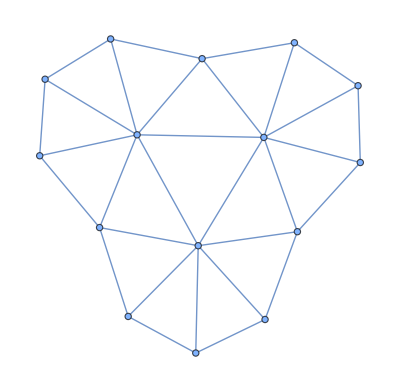

```mathematica
comS = "
import numpy as np
import scipy as sp
import hypertiling as ht
rez = []
T = ht.HyperbolicTiling(7,3,2, center='vertex')
nbrs = T.get_nbrs_list(method='RO')
A = ht.operators.adjacency(nbrs)
A.todense()"; (*center=vertex size 8 -> +???mins, n=4->size=85 is a bit small*)
adMat =Normal@ExternalEvaluate[s,comS];//AbsoluteTiming
hypG37 = AdjacencyGraph[adMat]
```

{37.6752,Null}

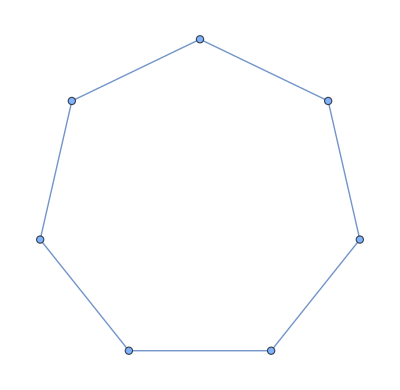

```mathematica
comS = "
import numpy as np
import scipy as sp
import hypertiling as ht
rez = []
T = ht.HyperbolicTiling(3,7,1, center='vertex')
nbrs = T.get_nbrs_list(method='RO')
A = ht.operators.adjacency(nbrs)
A.todense()"; (*center=vertex size 8 -> +???mins, n=4->size=85 is a bit small*)
adMat =Normal@ExternalEvaluate[s,comS];//AbsoluteTiming
hypG73a = AdjacencyGraph[adMat]
```

{0.0339529,Null}

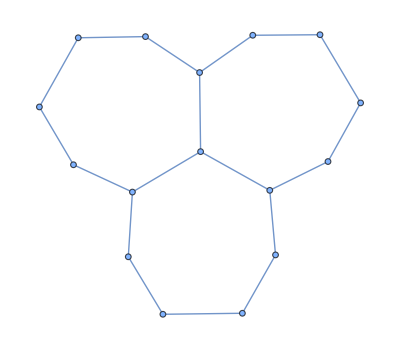

```mathematica
comS = "
import numpy as np
import scipy as sp
import hypertiling as ht
rez = []
T = ht.HyperbolicTiling(3,7,2)
nbrs = T.get_nbrs_list(method='RO')
A = ht.operators.adjacency(nbrs)
A.todense()"; (*center=vertex size 8 -> +???mins, n=4->size=85 is a bit small*)
adMat1 =Normal@ExternalEvaluate[s,comS];//AbsoluteTiming
hypG73b = AdjacencyGraph[adMat1, GraphLayout->"HighDimensionalEmbedding"]
```

```mathematica
layoutNames={"SpringElectricalEmbedding","SpringEmbedding","HighDimensionalEmbedding","SpectralEmbedding","CircularEmbedding","SpiralEmbedding","StarEmbedding","RadialEmbedding","LayeredDigraphEmbedding","PlanarEmbedding","LinearEmbedding","GridEmbedding"};

Table[AdjacencyGraph[adMat1,GraphLayout->l,PlotLabel->l],{l,layoutNames}]
```

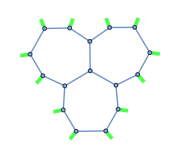

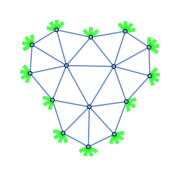

```mathematica
pgA =addGreen[hypG73b,3]
pgB =addGreen[hypG37,7]
(*pgC =addGreen[hypG73a,3]*)
```

```mathematica
dataPathListH = 
{
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\plotData\\hyp73_size2_center_v2.csv",
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\plotData\\hyp37size2.csv",
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\plotData\\hyp73_size1.csv",
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\plotData\\box_2x2x3.csv"
};
niuListH = {3,7,3,6};
titleListH = {"{p,q} = {7,3}", "{p,q} = {3,7}","{7,3} @ 7 sites","2 x 2 x 3 grid"}
targetNs = { 16,15,7,12}
```

{{p,q} = {7,3},{p,q} = {3,7},{7,3} @ 7 sites,2 x 2 x 3 grid}

{16,15,7,12}

```mathematica
Table[makePlotI[i, dataPathListH,niuListH,titleListH,targetNs[[i]]],{i,Length@dataPathListH}]
```

```mathematica
ps = Table[makePlotI[i, dataPathListH,niuListH,titleListH,targetNs[[i]]],{i,2}];
gs = {pgA,pgB};
lg = SwatchLegend[
cols,
Style[#,16,FontFamily->"Times New Roman"]&/@{"MI ","SF ","SF^*"},LegendFunction->"Frame",Background->White];
imsize = 220*2-60;
plot = Rasterize[#,ImageResolution->300,ImageSize->imsize]&@GraphicsGrid[{gs,ps},Spacings->{-30,0},Epilog->{Inset[lg,Scaled[{1.35,-0.12}]]},ImageSize->imsize]
(*Make ticks smaller?*)
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs_svg\\homo_MI_SF_hyper.svg",plot]
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\homo_MI_SF_hyper.pdf",plot]
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\homo_MI_SF_hyper.png",plot]
```

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs_svg\homo_MI_SF_hyper.svg

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs\homo_MI_SF_hyper.pdf

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs\homo_MI_SF_hyper.png

```mathematica
lg = SwatchLegend[
cols,
Style[#,16,FontFamily->"Times New Roman"]&/@{"|Φ| = 0","|Φ| > 0","n > 1"},
(*LegendLabel->Style["Fitted functions",12,FontFamily->"Times New Roman"],*)LegendFunction->"Frame"
]
```

```mathematica
cols = {Black,Yellow,Yellow};
ps = Table[makePlotI[i, dataPathListH,niuListH,titleListH,targetNs[[i]]],{i,2}];
cols = {Black,Yellow,RGBColor[1,0.86,0]};
gs = {pgA,pgB};
lg = SwatchLegend[
cols,
Style[#,16,FontFamily->"Times New Roman"]&/@{"MI ","SF "},LegendFunction->"Frame",Background->White];
imsize = 220*2-60 + 30;
plot = Rasterize[#,ImageResolution->300,ImageSize->imsize]&@GraphicsGrid[{gs,ps},Spacings->{0,0},Epilog->{Inset[lg,Scaled[{1.28,-0.17}]]},ImageSize->imsize]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs_svg\\simple_homo_MI_SF_hyper.svg",plot]
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\simple_homo_MI_SF_hyper.pdf",plot]
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\simple_homo_MI_SF_hyper.png",plot]
```

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs_svg\simple_homo_MI_SF_hyper.svg

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs\simple_homo_MI_SF_hyper.pdf

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs\simple_homo_MI_SF_hyper.png

### Lattice graphs

```mathematica
carpet[n_]:=(*Mr.Wizard*)Nest[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,1,n];
carpetGraph[n_]:=Module[{sa,edges,parts,onesPositions},parts={{1,0},{0,1}};
sa=SparseArray@carpet[n];
onesPositions=sa["NonzeroPositions"];
edges=Flatten[With[{m=ArrayPad[sa,1]},Function[pos,pos->#&/@Pick[pos+#&/@parts,Extract[m,1+pos+#&/@parts],1]]/@onesPositions],1];
Graph[onesPositions,edges,VertexCoordinates->onesPositions,DirectedEdges->False]]
```

```mathematica
tetraGraph[n_]:=Block[{},
Quiet@NearestNeighborGraph[Append[Flatten[Table [Block[{pts},
pts = N@GraphEmbedding[ResourceFunction["TriangularGridGraph"][i]];
pts = Transpose[Transpose[pts]-Mean/@Transpose[pts]];
pts =N@ {#1,#2,-i*Sqrt[6]/3}&@@@pts
],{i,n}],1],{0,0,0}],{12,1.1},WorkingPrecision->10]
]
tetraAdMat[n_]:= tetraAdMat[n]= N@AdjacencyMatrix[tetraGraph[n]]
```

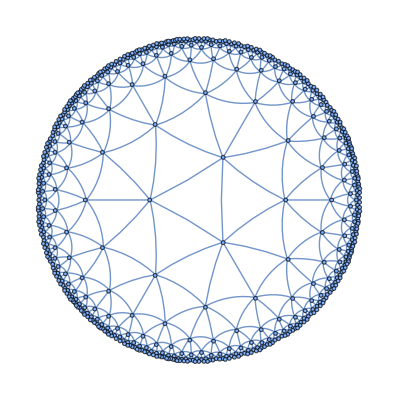

```mathematica
Graph[hyperbolicGraph[3,7,10],VertexSize->2]
```

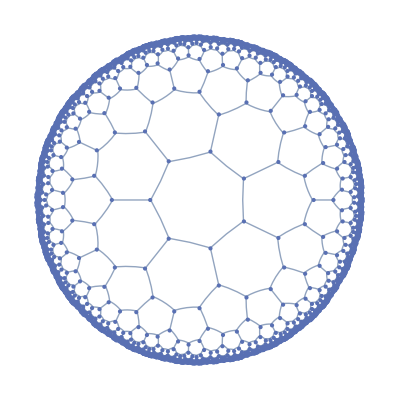

```mathematica
hyperbolicGraph[7,3,5]
```

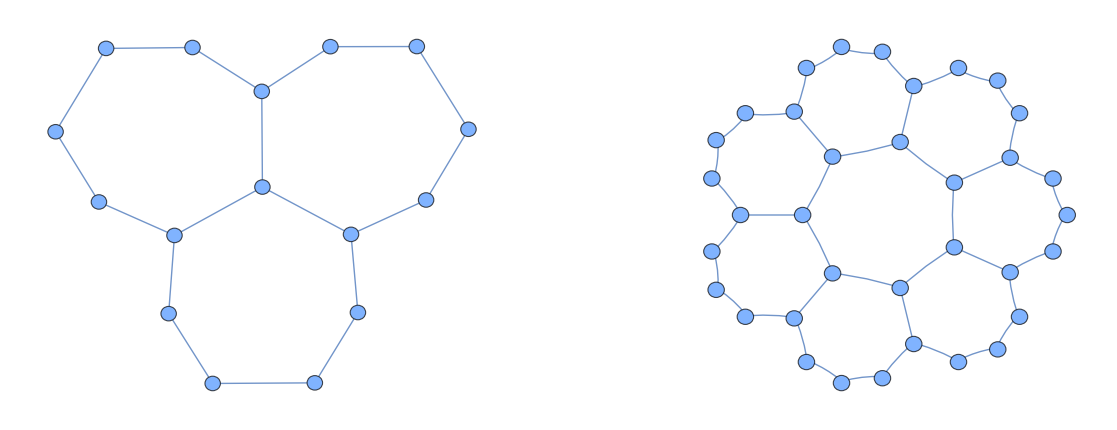

```mathematica
pHyp73Gs=GraphicsRow[{Graph[hypG73b,VertexSize->0.185,ImageSize->{Automatic,200}],Graph[hyperbolicGraph[7,3,1],ImageSize->{Automatic,200},VertexSize->0.4]},Spacings->60,Epilog->{Inset[Style["(a)",FontFamily->"Times New Roman",FontSize->28],Scaled[{0.02,0.96}],{Left,Top}],
Inset[Style["(b)",FontFamily->"Times New Roman",FontSize->28],Scaled[{0.58,0.96}],{Left,Top}]}]
```

```mathematica
{im1,im2,im3,im4} = ImageCrop[#,1220]&/@Import/@
{"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\pyCode\\overleafHyperpng\\7_3_1.png",
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\pyCode\\overleafHyperpng\\7_3_2.png",
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\pyCode\\overleafHyperpng\\3_7_1.png",
"C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\pyCode\\overleafHyperpng\\3_7_2.png"}
```

```mathematica
pHyp73Gs=GraphicsRow[{im1,im2,im4},Epilog->{
Inset[Style["(a)",FontFamily->"Times New Roman",FontSize->28],Scaled[{0.,0.96}],{Left,Top}],
Inset[Style["(b)",FontFamily->"Times New Roman",FontSize->28],Scaled[{0.33,0.96}],{Left,Top}],
Inset[Style["(c)",FontFamily->"Times New Roman",FontSize->28],Scaled[{0.66,0.96}],{Left,Top}]}]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\hyp73graphs.png",pHyp73Gs]
```

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs\hyp73graphs.png

```mathematica
grid1 = GraphicsGrid[{Graph[#,VertexSize->0.5]&/@{Graph[MeshConnectivityGraph[SierpinskiMesh[5]],VertexSize-> .25,ImageSize->{Automatic,150}],Graph[carpetGraph[3],ImageSize->{Automatic,150}]},Graph[#,VertexSize->0.5]&/@{Graph[ResourceFunction["TriangularGridGraph"][33],ImageSize->{Automatic,150}],GridGraph[{27,27},ImageSize->{Automatic,150}]}},ImageSize->{Automatic,300}]
```

```mathematica
column1A = GraphicsColumn[Graph[#,VertexSize->0.5]&/@{Graph[MeshConnectivityGraph[SierpinskiMesh[5]],VertexSize-> .25,ImageSize->{Automatic,150}],Graph[ResourceFunction["TriangularGridGraph"][33],ImageSize->{Automatic,150}]},ImageSize->{Automatic,300}]
column1B = GraphicsColumn[Graph[#,VertexSize->0.5]&/@{Graph[carpetGraph[3],ImageSize->{Automatic,150}],GridGraph[{27,27},ImageSize->{Automatic,150}]},ImageSize->{Automatic,300}]
```

```mathematica
AbsoluteOptions[grid1,ImageSize][[1,2,2]]
```

324.639

```mathematica
VertexCount/@(Graph[#,VertexSize->0.7,ImageSize->250]&/@{hyperbolicGraph[3,7,6],hyperbolicGraph[7,3,2]})
```

{96,112}

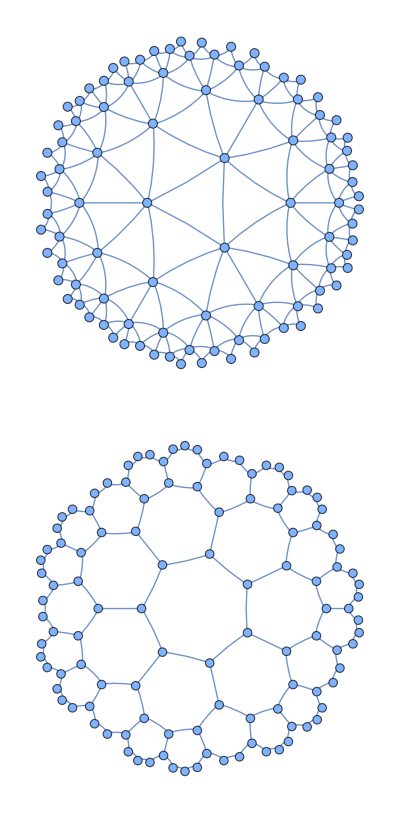

```mathematica
grid3 = GraphicsColumn[Graph[#,VertexSize->0.7,ImageSize->250]&/@{hyperbolicGraph[3,7,6],hyperbolicGraph[7,3,2]},ImageSize->{Automatic,300},Spacings->-1]
```

```mathematica
grid4= Graphics@GraphicsColumn[Reverse@{im1,im3},ImageSize->{Automatic,300},Spacings->0]
```

-Graphics-

```mathematica
gSierpTet=Rasterize[GraphPlot3D[MeshConnectivityGraph[SierpinskiMesh[4,3]],VertexSize->0.2,ImageSize->{Automatic,AbsoluteOptions[grid1,ImageSize][[1,2,2]]},PlotRangePadding->{Automatic,0.4}],ImageResolution->300,ImageSize->{Automatic,150}]
```

-Graphics-

```mathematica
gTetra=Rasterize[GraphPlot3D[tetraGraph[12],VertexSize->0.2,ImageSize->{Automatic,AbsoluteOptions[grid1,ImageSize][[1,2,2]]},ViewPoint->{1.3,-2.4,2.},ImageSize->{Automatic,250},PlotRangePadding->{Automatic,7}],ImageResolution->300,ImageSize->{Automatic,150}]
```

-Graphics-

```mathematica
grid2 =  GraphicsColumn[{gSierpTet,gTetra},ImageSize->{Automatic,300},Spacings->0]
```

```mathematica
(AbsoluteOptions[#,ImageSize][[1,2]]&/@{grid1,grid2,grid3,grid4,column1A,column1B,gridA})
```

{{322.07,300.},{146.259,300.},{161.91,300.},{164.432,300.},{182.402,300.},{159.545,300.},{560.,308.542}}

```mathematica
Total@(AbsoluteOptions[#,ImageSize][[1,2]]&/@{grid2,grid3,grid4,column1A,column1B})
```

{814.548,1500.}

```mathematica
(AbsoluteOptions[#,ImageSize][[1,2]]&/@{column1A,column1B,grid2,grid3})
```

{{182.402,300.},{159.545,300.},{146.259,300.},{161.91,300.}}

```mathematica
gridA = GraphicsRow[Rasterize[#,ImageResolution->300]&/@{column1A,column1B,grid2,grid3,grid4},Spacings->-3,ImageSize->{Automatic,300},
Epilog->{Inset[Style["(a)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.03,0.97}],{Left,Top}],
Inset[Style["(b)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.03,0.5}],{Left,Top}],
Inset[Style["(c)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.18,0.97}],{Left,Top}],
Inset[Style["(d)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.18,0.5}],{Left,Top}],
Inset[Style["(e)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.44,0.97}],{Left,Top}],
Inset[Style["(f)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.44,0.5}],{Left,Top}],
Inset[Style["(g)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.59,0.97}],{Left,Top}],
Inset[Style["(h)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.59,0.5}],{Left,Top}],
Inset[Style["(i)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.79,0.97}],{Left,Top}],
Inset[Style["(j)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.79,0.5}],{Left,Top}]
}]
```

-Graphics-

```mathematica
gridFin = GraphicsRow[{grid1,gridB},
Epilog->{Inset[Style["(a)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.03,0.97}],{Left,Top}],
Inset[Style["(b)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.03,0.5}],{Left,Top}],
Inset[Style["(c)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.15,0.97}],{Left,Top}],
Inset[Style["(d)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.15,0.5}],{Left,Top}],
Inset[Style["(e)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.38,0.75}],{Left,Top}],
Inset[Style["(f)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.62,0.75}],{Left,Top}],
Inset[Style["(g)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.815,0.97}],{Left,Top}],
Inset[Style["(h)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.825,0.525}],{Left,Top}]
}]
```

-Graphics-

```mathematica
gridFin = GraphicsRow[{grid1,gSierpTet,gTetra,grid2},
Epilog->{Inset[Style["(a)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.03,0.97}],{Left,Top}],
Inset[Style["(b)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.03,0.5}],{Left,Top}],
Inset[Style["(c)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.15,0.97}],{Left,Top}],
Inset[Style["(d)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.15,0.5}],{Left,Top}],
Inset[Style["(e)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.38,0.75}],{Left,Top}],
Inset[Style["(f)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.62,0.75}],{Left,Top}],
Inset[Style["(g)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.815,0.97}],{Left,Top}],
Inset[Style["(h)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.825,0.525}],{Left,Top}]
},

ImageSize->{Automatic,300},Spacings->0.2]
```

-Graphics-

```mathematica
gridFin = GraphicsRow[{grid1,GraphPlot3D[MeshConnectivityGraph[SierpinskiMesh[4,3]],VertexSize->0.2,ImageSize->{Automatic,AbsoluteOptions[grid1,ImageSize][[1,2,2]]}]},
Epilog->{Inset[Style["(a)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.03,0.95}],{Left,Top}],
Inset[Style["(b)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.26,0.95}],{Left,Top}],
Inset[Style["(d)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.03,0.55}],{Left,Top}],
Inset[Style["(e)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.26,0.55}],{Left,Top}],
Inset[Style["(c)",FontFamily->"Times New Roman",FontSize->25],Scaled[{0.70,0.95}],{Left,Top}]}]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\latticeGraphs.png",gridA,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\latticeGraphs.pdf",gridFin];
```

```mathematica
s
```

#### Do hyperbolics have a hausdorff dimension?

```mathematica
ttt=Table[Block[{comS,gg},comS = "
import numpy as np
import scipy as sp
import hypertiling as ht
rez = []
T = ht.HyperbolicTiling(3,7,"<>ToString[n]<>")
nbrs = T.get_nbrs_list(method='RO')
A = ht.operators.adjacency(nbrs)
A.todense()"; (*center=vertex size 8 -> +???mins, n=4->size=85 is a bit small*)
adMat1 =Normal@ExternalEvaluate[s,comS];
gg = AdjacencyGraph[adMat1];
{N@GraphDiameter[gg],VertexCount@gg}],{n,2,7}]
```

{{6.,16},{11.,61},{16.,181},{21.,496},{26.,1321},{31.,3481}}

```mathematica
Remove[d]
```

```mathematica
ttt2=Table[Block[{comS,gg},gg = MeshConnectivityGraph@SierpinskiMesh[n];
{N@GraphDiameter[gg],VertexCount@gg}],{n,3,8}]
```

{{8.,42},{16.,123},{32.,366},{64.,1095},{128.,3282},{256.,9843}}

```mathematica
ttt3=Table[Block[{comS,gg},comS = "
import numpy as np
import scipy as sp
import hypertiling as ht
rez = []
T = ht.HyperbolicTiling(7,3,"<>ToString[n]<>")
nbrs = T.get_nbrs_list(method='RO')
A = ht.operators.adjacency(nbrs)
A.todense()"; (*center=vertex size 8 -> +???mins, n=4->size=85 is a bit small*)
adMat1 =Normal@ExternalEvaluate[s,comS];
gg = AdjacencyGraph[adMat1];
{N@GraphDiameter[gg],VertexCount@gg}],{n,3,8}]
```

{{4.,29},{6.,85},{8.,232},{10.,617},{12.,1625},{14.,4264}}

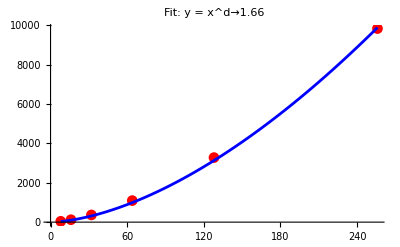

```mathematica
fit=NonlinearModelFit[ttt,x^d,{{d,2}},x];

(*Extract the fitted exponent*)
dval=fit["BestFitParameters"][[1]];

(*Plot the data and the fit*)
Show[ListPlot[ttt,PlotStyle->Red,PlotMarkers->Automatic],Plot[fit[x],{x,Min[ttt[[All,1]]],Max[ttt[[All,1]]]},PlotStyle->Blue],PlotLabel->Row[{"Fit: y = x^",NumberForm[dval,{3,2}]}]]
```

```mathematica
N@GraphDiameter[hypG73bTEST]/VertexCount@hypG73bTEST
```

0.180328

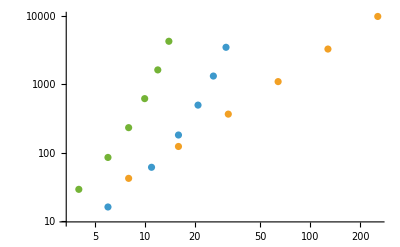

```mathematica
ListLogLogPlot[{ttt,ttt2,ttt3}]
```

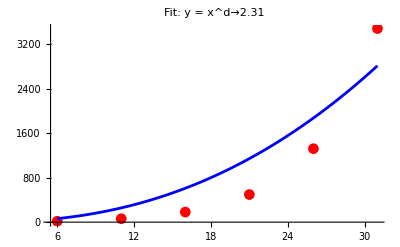

```mathematica
fit=NonlinearModelFit[ttt,x^d,{{d,2}},x];

(*Extract the fitted exponent*)
dval=fit["BestFitParameters"][[1]];

(*Plot the data and the fit*)
Show[ListPlot[ttt,PlotStyle->Red,PlotMarkers->Automatic],Plot[fit[x],{x,Min[ttt[[All,1]]],Max[ttt[[All,1]]]},PlotStyle->Blue],PlotLabel->Row[{"Fit: y = x^",NumberForm[dval,{3,2}]}]]
```

```mathematica
eTest = Eigenvalues[-N@AdjacencyMatrix@carpetGraph[4]];
```

Eigenvalues::arh: Because finding 4096 out of the 4096 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

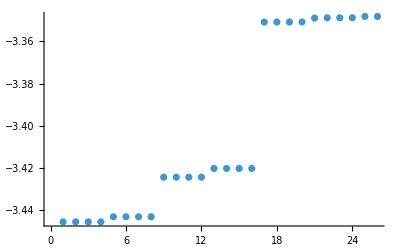

```mathematica
ListPlot[Sort[eTest][[;;26]]]
```

### Other approach

```mathematica
mu = (1 + delta)U
```

```mathematica
0== (1-mu)+ gsEnergy*J*2+J^2*(9/2*theSumA -gsEnergy^2*2)+ 2*J^3*(3*gsEnergy^3- (25/4+7/2)*gsEnergy*theSumA - 6*theSumB);
```

```mathematica
0==mu+ gsEnergy*J+J^2*(6*theSumA -gsEnergy^2*2)+ 2*J^3*(3*gsEnergy^3- (25/4+7/4)*gsEnergy*theSumA - 6*theSumB);
```

```mathematica
2*N@EdgeCount[#]/VertexCount[#]&@GridGraph[{100,100,100}]
```

5.94

```mathematica
First/@ Eigensystem[-N@AdjacencyMatrix@GridGraph[{10,10}],1,Method->{"Arnoldi","Criteria"->"RealPart","Shift"->-4*1.2,MaxIterations->10000}];
```

Eigensystem::wrgopt: The value -1.2 zz of the option Shift is incorrect.

First::normal: Nonatomic expression expected at position 1 in First[1].

Eigensystem::nonopt: Options expected (instead of Method) beyond position 2 in …. An option must be a rule or a list of rules.

```mathematica
dataThird[adMat_]:=Block[{zz=Ceiling[Total[Total@adMat]/Length@adMat],gsEnergy,gsVec,theSumA,theSumB,eq1,eq2,s1,s2,d1,d2},
{gsEnergy,gsVec} =First/@ Eigensystem[-adMat,1,Method->{"Arnoldi","Criteria"->"RealPart","Shift"->-zz*1.1,MaxIterations->20000}];
Print[StringForm["E = `` @ z = ``",gsEnergy,zz]];
theSumA = Sum[adMat[[i,j]]^2*gsVec[[j]]^2,{i,Length@adMat},{j,Length@adMat}];
theSumB = Sum[adMat[[i,j]]^3*gsVec[[i]]*gsVec[[j]],{i,Length@adMat},{j,Length@adMat}];
eq1 = (1-mu)+ gsEnergy*J*2+J^2*(9/2*theSumA -gsEnergy^2*2)+ 2*J^3*(3*gsEnergy^3- (25/4+7/2)*gsEnergy*theSumA - 6*theSumB);
eq2 = mu+ gsEnergy*J+J^2*(6*theSumA -gsEnergy^2*2)+ 2*J^3*(3*gsEnergy^3- (25/4+11/4)*gsEnergy*theSumA - 6*theSumB);
s1 = Solve[eq1==0,J,Reals];

s2 = Solve[eq2==0,J,Reals];
Return[Table[{zz*Min@Select[Union[Select[(J/.s1),NumericQ],Select[(J/.s2),NumericQ]],#>=0&],mu},{mu,0.,1,0.01}]];
];
```

```mathematica
plotThird[data_]:=ListLinePlot[data,PlotStyle-> Directive[Magenta,Thickness[0.018]]]
```

```mathematica
Length
```

```mathematica
gList = {GridGraph[{1,3282}],MeshConnectivityGraph@SierpinskiMesh[7],ResourceFunction["TriangularGridGraph"][80]};
VertexCount/@gList
```

{3282,3282,3321}

```mathematica
dataBlue = Table[dataThird[N@AdjacencyMatrix@ggraph],{ggraph,gList}];//AbsoluteTiming
```

E = -2. @ z = 2

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

E = -3.99987 @ z = 4

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

E = -5.98854 @ z = 6

{120.245,Null}

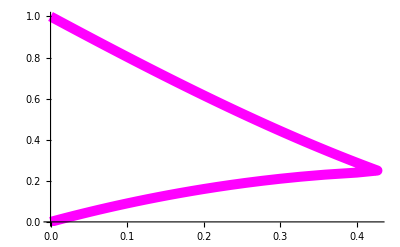
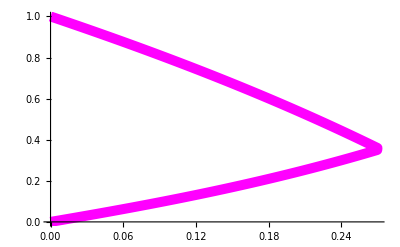
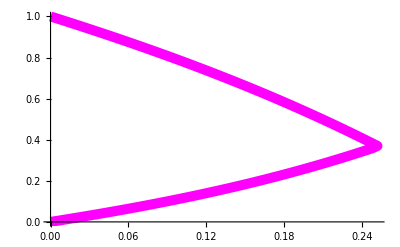

```mathematica
psBlue = plotThird/@dataBlue
```

```mathematica
cols = {Black,Yellow,Yellow};
ps1 = Table[makePlotI[i],{i,3}];
ps = Table[Show[ps1[[i]],psBlue[[i]]],{i,3}];
cols = {Black,Yellow,RGBColor[1,0.86,0]};
gs = {pg1,pg2,pg3};
lg = SwatchLegend[
{Black,Yellow,Magenta},
Style[#,16,FontFamily->"Times New Roman"]&/@{"MI ","SF ","SC "},LegendFunction->"Frame",Background->White,LegendMarkers->{"Square","Square","Line"},LegendMargins->4];
plot = Rasterize[#,ImageResolution->300]&@GraphicsGrid[{gs,ps},Spacings->{{0,-30,-30,0},{0,0,0}},Epilog->{Inset[lg,Scaled[{0.978,0.17}],{Right,Bottom}]},ImageSize->220*3-100]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\MI_SF_third_Correction.pdf",plot]
```

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs\MI_SF_third_Correction.pdf

```mathematica
s=StartExternalSession["Python"]
```

ExternalSessionObject[…]

```mathematica
comS = "
import numpy as np
import scipy as sp
import hypertiling as ht
rez = []
T = ht.HyperbolicTiling(7,3,8)
nbrs = T.get_nbrs_list(method='RO')
A = ht.operators.adjacency(nbrs)
A.todense()"; (*center=vertex size 8 -> +???mins, n=4->size=85 is a bit small*)
adMat37 =Normal@ExternalEvaluate[s,comS];//AbsoluteTiming
Length@adMat37
```

{1.37171,Null}

4264

```mathematica
comS = "
import numpy as np
import scipy as sp
import hypertiling as ht
rez = []
T = ht.HyperbolicTiling(3,7,7, center='vertex')
nbrs = T.get_nbrs_list(method='RO')
A = ht.operators.adjacency(nbrs)
A.todense()"; (*center=vertex size 8 -> +???mins, n=4->size=85 is a bit small*)
adMat73 =Normal@ExternalEvaluate[s,comS];//AbsoluteTiming
Length@adMat73
```

{3.44207,Null}

5887

```mathematica
dataBlueHyp = Table[dataThird[N@adm],{adm,{adMat73,adMat37}}];//AbsoluteTiming
```

E = -2.90525 @ z = 3

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

E = -5.49119 @ z = 5

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{158.347,Null}

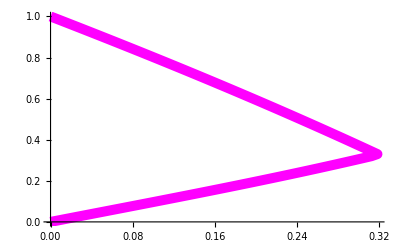
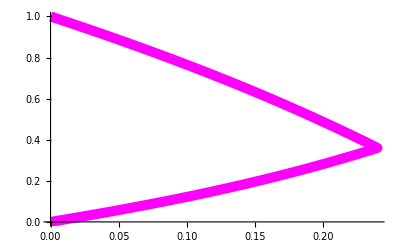

```mathematica
psBlueHyp = plotThird/@dataBlueHyp
```

```mathematica
(*make pgA and pgB in hyp section*)
```

```mathematica
Graphics[{Black,Rectangle[{0,0},{1,0.2}]},ImageSize->100]
```

-Graphics-

```mathematica
cols = {Black,Yellow,Yellow};
ps1 = Table[makePlotI[i, dataPathListH,niuListH,titleListH,targetNs[[i]]],{i,2}];
ps = Table[Show[ps1[[i]],psBlueHyp[[i]]],{i,2}];
cols = {Black,Yellow,RGBColor[1,0.86,0]};
gs = {pgA,pgB};
lg = SwatchLegend[
{Black,Yellow,Magenta},
Style[#,16,FontFamily->"Times New Roman"]&/@{"MI ","SF ","SC "},LegendFunction->"Frame",Background->White,LegendMarkers->{"Square","Square","Line"},LegendMargins->4];
lg2 = SwatchLegend[
{Magenta,Black,Yellow},
Style[#,16,FontFamily->"Times New Roman"]&/@{"SC ","MI ","SF "},LegendFunction->"Frame",Background->White,LegendMarkers->{"Line","Square","Square"}];
imsize = 220*2-60 + 30;
plotHyp = Rasterize[#,ImageResolution->300,ImageSize->imsize]&@GraphicsGrid[{gs,ps},Spacings->{0,0},Epilog->{Inset[lg,Scaled[{0.968,0.162}],{Right,Bottom}]},ImageSize->imsize]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\DIPCwork\\overleaf\\paperfigs\\MI_SF_third_Correction_Hyp.pdf",plotHyp]
```

C:\Users\kamil\OneDrive\Documents\DIPCwork\overleaf\paperfigs\MI_SF_third_Correction_Hyp.pdf

```mathematica
gList = {GridGraph[{1,1000}],ResourceFunction["TriangularGridGraph"][40],MeshConnectivityGraph@SierpinskiMesh[4]};
```

```mathematica
N@Total@Total[#]/Length[#]&@AdjacencyMatrix[gList[[1]]]
```

1.998